```mathematica
ℏ=1.0*10^-34;
kb=1.38*10^-23;
T0=6.4*10^-6;
ωt=2π *10.^5;
m171=170.936*(1.660539*10^-27);
```

```mathematica
Pn[n_,T_]:=E^(-ℏ ωt n/(kb T))(1-E^(-ℏ ωt/(kb T)))
```

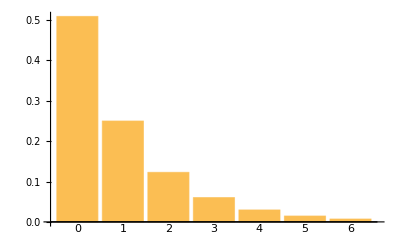

```mathematica
BarChart[Table[Pn[n,T0],{n,0,6}],ChartLabels->{"0","1","2","3","4","5","6"}]
```

## pi pulse n=0,1,2

define the motional space up to n=2

```mathematica
H0=({{ωe/2-Δ, Ω/2}, {Ω/2, ωg/2}});
H1=({{3/2 ωe-Δ, Ω/2}, {Ω/2, 3/2 ωg}});
H2=({{5/2 ωe-Δ, Ω/2}, {Ω/2, 5/2 ωg}});
Hc01=I η Ω/2({{1, 1}, {1, 1}});
Hc02=I η √2 Ω/2({{1, 1}, {1, 1}});
I1=({{1, 0}, {0, 1}});
```

```mathematica
H=ArrayFlatten[({{H2, Conjugate[Hc02], 0}, {Hc02, H1, Conjugate[Hc01]}, {0, Hc01, H0}})];
(*H=ArrayFlatten[({{I1, 0, 0}, {0, I1, 0}, {0, 0, H0}})];*)
MatrixForm[H]
```

(-Δ+(5 ωe)/2 | Ω/2 | -(ⅈ Conjugate[η Ω])/(√2) | -(ⅈ Conjugate[η Ω])/(√2) | 0 | 0
Ω/2 | (5 ωg)/2 | -(ⅈ Conjugate[η Ω])/(√2) | -(ⅈ Conjugate[η Ω])/(√2) | 0 | 0
(ⅈ η Ω)/(√2) | (ⅈ η Ω)/(√2) | -Δ+(3 ωe)/2 | Ω/2 | -1/2 ⅈ Conjugate[η Ω] | -1/2 ⅈ Conjugate[η Ω]
(ⅈ η Ω)/(√2) | (ⅈ η Ω)/(√2) | Ω/2 | (3 ωg)/2 | -1/2 ⅈ Conjugate[η Ω] | -1/2 ⅈ Conjugate[η Ω]
0 | 0 | (ⅈ η Ω)/2 | (ⅈ η Ω)/2 | -Δ+ωe/2 | Ω/2
0 | 0 | (ⅈ η Ω)/2 | (ⅈ η Ω)/2 | Ω/2 | ωg/2)

```mathematica
k=(2π)/(578.*10^-9);
ωR=(ℏ k^2)/(2 m171);
η0=√(ωR/ωt)
```

0.182014

```mathematica
Pns=Table[Pn[n,T0/2],{n,0,2}];
Pns[[3]]=1-Pns[[2]]-Pns[[1]];
```

```mathematica
Hn=H/.{ωe->ωt/2,ωg->ωt,Ω->5.*10^4,Δ->-ωt/4,η->η0};
ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,√Pns[[3]],0,√Pns[[2]],0,√Pns[[1]]}},ψ,{t,0,5./(5*10^4)}]
```

{{ψ→InterpolatingFunction[…]}}

```mathematica
(*Sum[Abs[Evaluate[ψ[t]/.ψs][[1,i]]]^2,{i,1,6}]*)
```

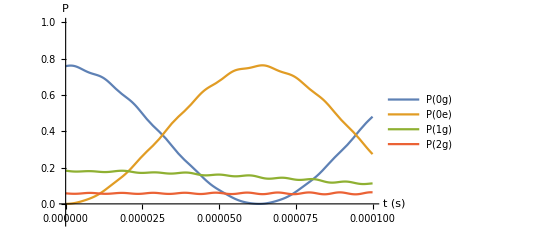

```mathematica
Plot[{Abs[Evaluate[ψ[t]/.ψs][[1,6]]]^2,Abs[Evaluate[ψ[t]/.ψs][[1,5]]]^2,Abs[Evaluate[ψ[t]/.ψs][[1,4]]]^2,Abs[Evaluate[ψ[t]/.ψs][[1,2]]]^2},{t,0,5./(5*10^4)},PlotRange->{-0.1,1},PlotLegends->{"P(0g)","P(0e)","P(1g)","P(2g)"},AxesLabel->{"t (s)","P"}]
```

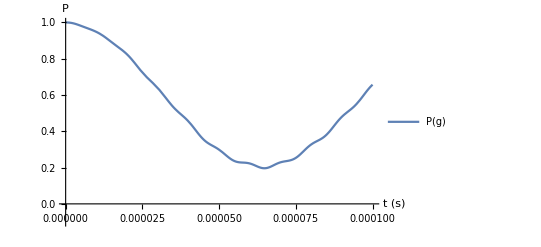

```mathematica
Plot[{Sum[Abs[Evaluate[ψ[t]/.ψs][[1,i]]]^2,{i,2,6,2}]},{t,0,5./(5*10^4)},PlotRange->{-0.1,1},PlotLegends->{"P(g)"},AxesLabel->{"t (s)","P"}]
```

## adiabatic transfer lamb dicke limit

```mathematica
Ht[t_]:=({{ωe/2+Δs((2*t)/Tp-1)+Δ0, Ω/2}, {Ω/2, ωg/2}});
MatrixForm[Ht[t]]
```

(Δ0+(-1+(2 t)/Tp) Δs+ωe/2 | Ω/2
Ω/2 | ωg/2)

```mathematica
Ttot=100./(5*10^4)
```

0.002

```mathematica
Htn[t_]:=Ht[t]/.{ωe->ωt/2,ωg->ωt,Ω->5.*10^4,Δ0->ωt/4,Δs->ωt,Tp->Ttot,η->η0};
ψs=NDSolve[{I ψ'[t]==Htn[t].ψ[t],ψ[0]=={0,1}},ψ,{t,0,Ttot}]
```

{{ψ→InterpolatingFunction[{{0., 0.002}}, <>]}}

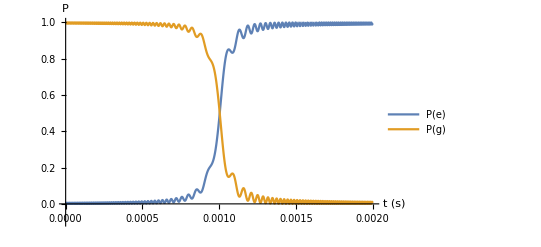

```mathematica
Plot[{Abs[Evaluate[ψ[t]/.ψs][[1,1]]]^2,Abs[Evaluate[ψ[t]/.ψs][[1,2]]]^2},{t,0,Ttot},PlotRange->{-0.1,1},AxesLabel->{"t (s)","P"},PlotLegends->{"P(e)","P(g)"}]
```

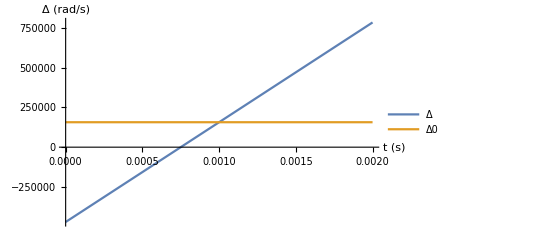

```mathematica
Plot[{(Δs((2*t)/Tp-1)+Δ0)/.{Δ0->ωt/4,Δs->ωt,Tp->Ttot},ωt/4},{t,0,Ttot},PlotLegends->{"Δ","Δ0"},AxesLabel->{"t (s)","Δ (rad/s)"}]
```

## adiabatic transfer w/ motional dephasing

```mathematica
Δadb[t_]:= Δs((2*t)/Tp-1)+Δ0
H0t[t_]:=({{ωe/2+Δadb[t], Ω/2}, {Ω/2, ωg/2}});
H1t[t_]:=({{3/2 ωe+Δadb[t], Ω/2}, {Ω/2, 3/2 ωg}});
H2t[t_]:=({{5/2 ωe+Δadb[t], Ω/2}, {Ω/2, 5/2 ωg}});
Hc01=I η Ω/2({{0, 1}, {1, 0}});
Hc02=I η √2 Ω/2({{0, 1}, {1, 0}});
```

```mathematica
Htadb[t_]:=ArrayFlatten[({{H2t[t], Conjugate[Hc02], 0}, {Hc02, H1t[t], Conjugate[Hc01]}, {0, Hc01, H0t[t]}})]
```

```mathematica
Ttot=1000./(1*10^4);
Htadbn[t_]:=Htadb[t]/.{ωe->ωt/2,ωg->ωt,Ω->1*10^4,Δ0->3 ωt/4,Δs->2ωt,Tp->Ttot,η->η0};
ψs=NDSolve[{I ψ'[t]==Htadbn[t].ψ[t],ψ[0]=={0,√Pns[[3]],0,√Pns[[2]],0,√Pns[[1]]}},ψ,{t,0,Ttot}]
```

{{ψ→InterpolatingFunction[{{0., 0.1}}, <>]}}

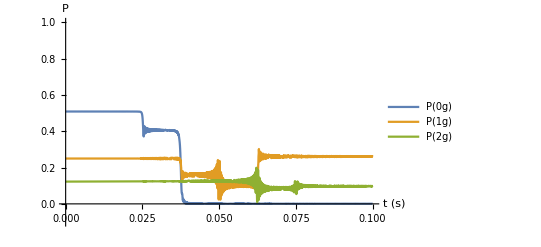

```mathematica
Plot[{Abs[Evaluate[ψ[t]/.ψs][[1,6]]]^2,Abs[Evaluate[ψ[t]/.ψs][[1,4]]]^2,Abs[Evaluate[ψ[t]/.ψs][[1,2]]]^2},{t,0,Ttot},PlotRange->{-0.1,1},PlotLegends->{"P(0g)","P(1g)","P(2g)"},AxesLabel->{"t (s)","P"}]
```

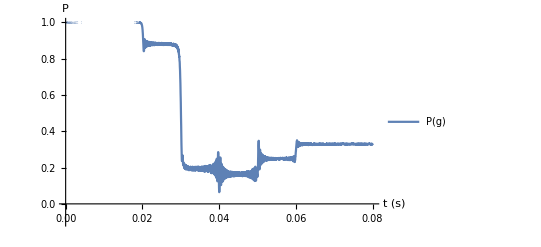

```mathematica
Plot[{Sum[Abs[Evaluate[ψ[t]/.ψs][[1,i]]]^2,{i,2,6,2}]},{t,0,Ttot},PlotRange->{-0.1,1},PlotLegends->{"P(g)"},AxesLabel->{"t (s)","P"}]
```

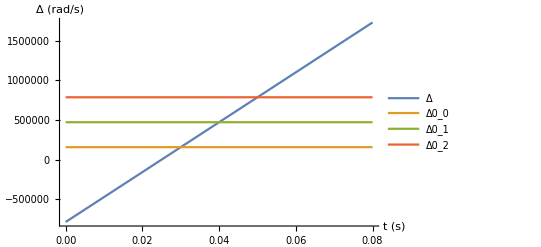

```mathematica
Plot[{Δadb[t]/.{Δ0->(3ωt)/4,Δs->2ωt,Tp->Ttot},ωt/4,(3ωt)/4,(5ωt)/4},{t,0,Ttot},PlotLegends->{"Δ","Δ0_0","Δ0_1","Δ0_2"},AxesLabel->{"t (s)","Δ (rad/s)"},PlotRange->All]
```

## successive pi pulses

```mathematica
Δadb[t_]:= Piecewise[{{(ωg-ωe)/2, 0≤t<π/Ω},{3*(ωg-ωe)/2, π/Ω≤t<2 π/Ω},{5*(ωg-ωe)/2,2 π/Ω≤t<3 π/Ω}}]
H0t[t_]:=({{ωe/2+Δadb[t], Ω/2}, {Ω/2, ωg/2}});
H1t[t_]:=({{3/2 ωe+Δadb[t], Ω/2}, {Ω/2, 3/2 ωg}});
H2t[t_]:=({{5/2 ωe+Δadb[t], Ω/2}, {Ω/2, 5/2 ωg}});
Hc01=I η Ω/2({{1, 1}, {1, 1}});
Hc02=I η √2 Ω/2({{1, 1}, {1, 1}});
Htpi[t_]:=ArrayFlatten[({{H2t[t], Conjugate[Hc02], 0}, {Hc02, H1t[t], Conjugate[Hc01]}, {0, Hc01, H0t[t]}})]
```

```mathematica
Ttot=(4π)/Ω/.{Ω->5*10^4};
Htpin[t_]:=Htpi[t]/.{ωe->ωt/2,ωg->ωt,Ω->5*10^4,η->η0};
```

```mathematica
ψs=NDSolve[{I ψ'[t]==Htadbn[t].ψ[t],ψ[0]=={0,√Pns[[3]],0,√Pns[[2]],0,√Pns[[1]]}},ψ,{t,0,Ttot}]
```

{{ψ→InterpolatingFunction[{{0., 0.000251327}}, <>]}}

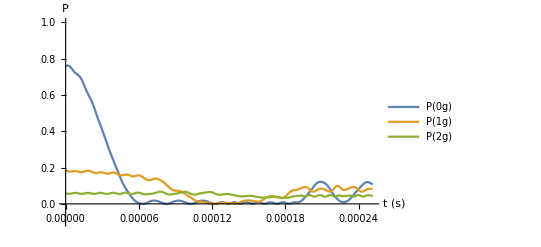

```mathematica
Plot[{Abs[Evaluate[ψ[t]/.ψs][[1,6]]]^2,Abs[Evaluate[ψ[t]/.ψs][[1,4]]]^2,Abs[Evaluate[ψ[t]/.ψs][[1,2]]]^2},{t,0,Ttot},PlotRange->{-0.1,1},PlotLegends->{"P(0g)","P(1g)","P(2g)"},AxesLabel->{"t (s)","P"}]
```

## lamb dicke limit

```mathematica
H=({{ωe-Δ, Ω/2}, {Ω/2, ωg}});
```

```mathematica
Hn=H/.{ωe->0.5*10^5,ωg->1.0*10^5,Ω->5.*10^4,Δ->-0.5*10^5};
```

```mathematica
ψs=NDSolve[{I ψ'[t]==Hn.ψ[t],ψ[0]=={0,1}},ψ,{t,0,5./(5*10^4)}]
```

{{ψ→InterpolatingFunction[…]}}

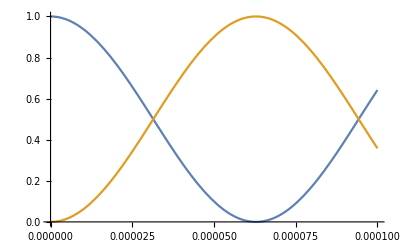

```mathematica
Plot[{Abs[Evaluate[ψ[t]/.ψs][[1,2]]]^2,Abs[Evaluate[ψ[t]/.ψs][[1,1]]]^2},{t,0,5./(5*10^4)}]
```

## motional overlap different trap freq

```mathematica
ψn[x_,y_,z_,n_,ω_]:=1/((2^n(n!))^(3/2)) Exp[-1/(2 ℏ)m171 ω (x^2+y^2+z^2)]HermiteH[n,√((m171 ω)/ℏ)x]HermiteH[n,√((m171 ω)/ℏ)y]HermiteH[n,√((m171 ω)/ℏ)z]
ψn1D[x_,n_,ω_]:=1/((2^n(n!))^(1/2))((m171 ω)/(π ℏ))^(1/4)Exp[-1/(2 ℏ)m171 ω (x^2)]HermiteH[n,√((m171 ω)/ℏ)x]
```

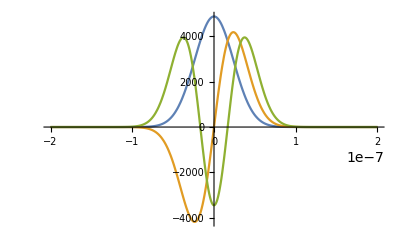

```mathematica
Plot[{ψn1D[x,0,ωt],ψn1D[x,1,ωt],ψn1D[x,2,ωt]},{x,-200*10^-9,200*10^-9},PlotRange->All]
```

```mathematica
Plot3D[ψn[x,y,0,2,ωt],{x,-1*10^-7,1*10^-7},{y,-1*10^-7,1*10^-7},PlotRange->All]
```

-Graphics3D-

```mathematica
ψnN[x_,y_,z_,nx_,ny_,nz_,ω_,m_]:=1/((2^(nx+ny+nz)(nx!)(ny!)(nz!))^(1/2)) ((m ω)/π)^(3/4)Exp[-1/2 m ω (x^2+y^2+z^2)]HermiteH[nx,√(m ω)x]HermiteH[ny,√(m ω)y]HermiteH[nz,√(m ω)z]
```

```mathematica
NIntegrate[ψnN[x,y,z,0,1.,1.]*ψnN[x,y,z,2,1/2.,1.],{x,-5,5},{y,-5,5},{z,-5,5},AccuracyGoal->5]
```

-0.0119873

```mathematica
Sum[Abs[NIntegrate[ψnN[x,y,z,0,1,1]*ψnN[x,y,z,nx,ny,nz,1/2,1],{x,-5,5},{y,-5,5},{z,-5,5},AccuracyGoal->5]]^2,{nx,0,6,2},{ny,0,6,2},{nz,0,6,2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

0.999869

```mathematica
NIntegrate[ψnN[x,y,z,0,0,0,1,1]*ψnN[x,y,z,0,2,0,1/2,1],{x,-5,5},{y,-5,5},{z,-5,5},AccuracyGoal->5]
```

-0.215774

```mathematica
10^4*100*10^-6
```

1

```mathematica
3.*10^8*6.626*10^-34/(0.548*1.602*10^-19)
```

2.26428×10^-6

```mathematica
1.1
```